```mathematica
Clear["Global`*"];
SeedRandom[0];
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"Sampler`";
Kq[p_,q_,r_]=0;
```

```mathematica
ρ=1-1/10^15;
SIGMA={{1,ρ},{ρ,1}};
U[x_,y_]=1/2 Simplify[{x,y}.LinearSolve[SIGMA,{x,y}]];
Uq[x_,y_]=D1[U[x,y],{x,y}];
Uqq[x_,y_]=D2[U[x,y],{x,y}];
Uqqq[x_,y_]=D3[U[x,y],{x,y}];
Dim=2;
```

```mathematica
SIGMA//MatrixForm
```

(1 | 999999999999999/1000000000000000
999999999999999/1000000000000000 | 1)

```mathematica
Dim=2;
BURNIN=5000;
ITERATIONS=10000;
```

```mathematica
QS=hmc[U,Uq,Uqq,Uqqq,Dim,BURNIN,ITERATIONS,{.5},{}];
```

10014.45097×10^122.714690.487320.4614124.343751{1}{4}{1.2719×10^-7}{4.45097×10^12}1.2719×10^-7FalseFalse

20024.75002×10^142.133610.2543230.1810821.734381{1}{4}{2.51638×10^-8}{4.75002×10^14}2.51638×10^-8FalseFalse

30032.90507×10^151.988780.3394540.5720673.21461{1,4}{1,4}{1.17391×10^-8}{2.90507×10^15}1.17391×10^-8FalseFalse

40047.53501×10^153.904420.3394430.3006281.003911{1}{4}{6.62641×10^-9}{7.53501×10^15}6.62641×10^-9FalseFalse

50052.32927×10^171.250280.1479340.2110812.314221{2,4}{1,4}{9.84973×10^-10}{2.32927×10^17}9.84973×10^-10FalseFalse

60062.32927×10^170.2456820.09653390.08843363.392581{2,4}{1,4}{9.84973×10^-10}{2.32927×10^17}9.84973×10^-10FalseFalse

70072.32927×10^172.4720.5900710.4838064.777341{2,4}{1,4}{9.84973×10^-10}{2.32927×10^17}9.84973×10^-10FalseFalse

80082.32927×10^171.308850.5514760.4216232.558591{2,4}{1,4}{9.84973×10^-10}{2.32927×10^17}9.84973×10^-10FalseFalse

90092.32927×10^171.914430.8056210.3366753.31251{2,4}{1,4}{9.84973×10^-10}{2.32927×10^17}9.84973×10^-10FalseFalse

{0.99964,1.0068}

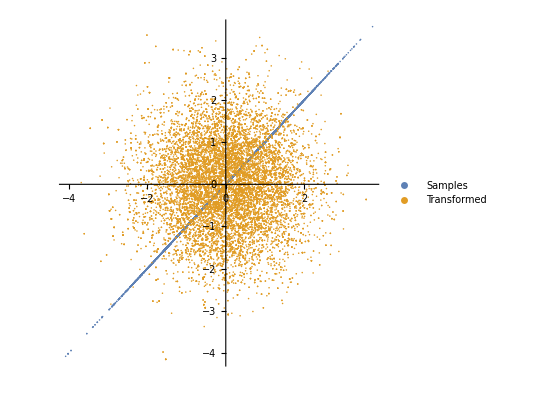

```mathematica
QS1=QS.MatrixPower[SIGMA,-.5];
StandardDeviation[QS1]
ListPlot[{QS,QS1},PlotStyle->Opacity[1],AspectRatio->1,PlotLegends->{Samples, Transformed}]
```